## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

```mathematica
<<MaTeX`
<<ErrorBarPlots`
```

## Equation and and Eigenvalue function

```mathematica
Eq=EqTeukolskyRadial/.RuleKRadial;
```

## Parameter rules and equation simplification

```mathematica
RuleRHorizon={R->Function[x,x^(-s-I χ/τ)f[x]]};
EquationF=PowerExpand@Simplify[x^(s+I χ/τ)x (x+τ) (Eq/.RuleRHorizon)];
(* all params *)
RuleBoundaryBH={𝒶[0]->1};
RuleParams={
τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),c->𝒥 ω̄/rp,ℰ𝓋->ℰ[s,l,m,c],
λ->c^2-2m c+ℰ𝓋-s(s+1),rp->1+√(1-𝒥^2),
ℬ->Sqrt[ξ^2-4 c^2+4m c],
ξ-> c^2-2m c+ℰ𝓋,
𝒞->Sqrt[(ξ^2+4c m -4 c^2)((ξ-2)^2+36c m -36 c^2)+(2ξ-1)(96 c^2-48m c)+(6 ω̄ τ)^2]
};
```

```mathematica
(* Function to replace all parameters accordingly *)
Clear[ReplaceParams]
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_]=#1//.RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}&;
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_,𝓌_]=#1//.RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}&;
```

## Equation solver definition

```mathematica
(* Coeficients to estimate f and f' close to BH horizon *)
nCoefH=6;
RuleFHorizon={f->Function[x,∑_(n=0)^nCoefH 𝒶[n] (x)^n]};
```

```mathematica
(* Coeficients to estimate Ain and Aout at infinity *)
nCoefInf=6;
RuleRinInf={R->Function[x,x^-1 ⅇ^(-ⅈ ω̄ x)(2 ω̄ x)^(-ⅈ (2-τ) ω̄) ∑_(n=0)^nCoefInf 𝒾[n] x^-n]};
RuleRoutInf={R->Function[x,x^(-1-2 s) ⅇ^(ⅈ ω̄ x)(2 ω̄ x)^(+ⅈ (2-τ) ω̄) ∑_(n=0)^nCoefInf ℴ[n] x^-n]};
```

```mathematica
(* OptionsPattern to use with SolveωF to get more precision/accuracy out of NDSolve *)
IncreasePrecision={PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8};
```

```mathematica
(* Information to include on CSV headers *)
metaRule={"xH"->10^(-12.),"fpH"->"1.0","fmH"->"1.0","nCoefH"->nCoefH,"nCoefInf"->nCoefInf};
headerZMetaRule={"headers"->{"J/M^2","omega*rp","Zphi0","Zphi2","Zphi0phi2"}};
headerϕMetaRule={"headers"->{"J/M^2","omega*rp","RE(Yin/Yhole)","IM(Yin/Yhole)","RE(Zout/Zhole)","IM(Zout/Zhole)"}};
headerϕ0MetaRule={"headers"->{"J/M^2","omega*rp","RE(Yin/Yhole)","IM(Yin/Yhole)","RE(Yout/Yhole)","IM(Yout/Yhole)"}};
headerϕ2MetaRule={"headers"->{"J/M^2","omega*rp","RE(Zin/Zhole)","IM(Zin/Zhole)","RE(Zout/Zhole)","IM(Zout/Zhole)"}};
```

#### Solver 1 (simpler)

```mathematica
Clear[SolveSingle];
SolveSingle[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝓌_?NumberQ,opts:OptionsPattern[]]/;0<𝒿<1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{x0,xINF,eqF,f0,fp0,fINF,ev},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF=2 π/Abs[𝓌]*200.;
ev=ℰ[𝓈,ℓ,𝓂,(𝒿 𝓌)/(1+Sqrt[1-𝒿^2])];
{eqF,fINF}={EquationF,f[xINF] ⅇ^(ⅈ(Sign[𝓈] ω̄ (xINF+(2-τ)Log[xINF])-χ/τ Log[xINF]))}//ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌];
{f0,fp0}={f[x0],f'[x0]}/.RuleFHorizon/.First@Solve[CoefficientList[eqF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
{𝒿,𝓌,fINF}/.First@(Echo[#,"Plot f: ",(Plot[Abs[f[x]]/.First[#]//Evaluate,{x,0,xINF},PlotRange->All,ImageSize->Large]&)]&)@NDSolve[{eqF==0,f0==f[x0],fp0==f'[x0]}/.{ℰ[__]->ev,𝒶[0]->1},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]]
];
```

#### Solver 2 (higher order corrections)

```mathematica
Clear[SolveBoth];
SolveBoth[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝓌_?NumberQ,opts:OptionsPattern[]]/;0<𝒿<1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{eqF,f0,fp0,coefInInf,coefOutInf,in,out,ev,x0,xINF},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF=2Pi/Abs[𝓌]*80.;
ev=ℰ[𝓈,ℓ,𝓂,(𝒿 𝓌)/(1+Sqrt[1-𝒿^2])];
eqF=EquationF//ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌];

{f0,fp0}={f[x0],f'[x0]}/.RuleFHorizon/.First@Solve[CoefficientList[eqF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
coefInInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(ⅈ ω̄ x) (2 ω̄ x)^(ⅈ ω̄ (2-τ)) Eq/.RuleRinInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[𝒾[n],{n,1,nCoefInf}]];
coefOutInf=First@Solve[0==Simplify@SeriesCoefficient[Series[x^(2 s) ⅇ^(-ⅈ ω̄ x) (2 ω̄ x)^(-ⅈ ω̄ (2-τ)) Eq/.RuleRoutInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[ℴ[n],{n,1,nCoefInf}]];
{in,out}=Total@ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌][{R[x]/.RuleRinInf/.coefInInf,R[x]/.RuleRoutInf/.coefOutInf}]//{𝒾[0],ℴ[0]}/.First@Solve[{#==RInf,D[#,x]==RpInf}/.{x->xINF,ℰ[__]->ev},{𝒾[0],ℴ[0]}]&;
 
{𝒿,𝓌,in,out}/.ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌][{RInf->R[xINF],RpInf->R'[xINF]}/.RuleRHorizon]/.First@NDSolve[{eqF==0,f0==f[x0],fp0==f'[x0]}/.{ℰ[__]->ev,𝒶[0]->1},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]]
];
```

## Export data

```mathematica
Clear[FormatZSingle,FormatZBoth,Formatϕ]
FormatZSingle[1|-1,ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2)/(χ Abs[#3]^2),-1/(1+(ℬ^2 τ^2 Abs[#4]^2)/(4 χ ω̄(τ^2+ 4 χ^2))),(ℬ^2 τ^4)/(4 χ^2 (τ^2+4 χ^2))Abs[#4/#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
FormatZBoth[+1,ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2)/(χ Abs[#3]^2),-1/(1+(16 χ (ω̄)^3 Abs[#4]^2)/(τ^2 ℬ^2)) ,((16 (ω̄)^4)/ℬ^2)Abs[#4/#3]^2-1}//ReplaceParams[#1,+1,ℓ,𝓂,#2])&;
FormatZBoth[-1,ℓ_,𝓂_]:=({#1,#2,-(χ(τ^2+ 4 χ^2))/(4 (ω̄)^3 τ^2 Abs[#3]^2),-1/(1+(ℬ^2 τ^2 Abs[#4]^2)/(4 χ ω̄ (τ^2+4 χ^2))),(ℬ^2/(16 (ω̄)^4))Abs[#4/#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
FormatZBoth[2,ℓ_,𝓂_]:=({#1,#2,-(4 (ω̄)^3 τ^4)/(χ (τ^2+4 χ^2) Abs[#3]^2),-1/(1+(64χ (τ^2+4 χ^2)  (ω̄)^5 Abs[#4]^2)/(𝒞^2 τ^4)) ,((256(ω̄)^8)/𝒞^2)Abs[#4/#3]^2-1}//ReplaceParams[#1,2,ℓ,𝓂,#2])&;
FormatZBoth[-2,ℓ_,𝓂_]:=({#1,#2,-(χ (τ^2+χ^2) (τ^2+4 χ^2))/(4  (ω̄)^5 τ^4 Abs[#3]^2),-1/(1+(𝒞^2 τ^4 Abs[#4]^2)/(64 χ (τ^2+χ^2) (τ^2+4 χ^2) (ω̄)^3)),( 𝒞^2/(256(ω̄)^8))Abs[#4/#3]^2-1}//ReplaceParams[#1,-2,ℓ,𝓂,#2])&;
Formatϕ={#1,#2,Re[#3],Im[#3],Re[#4],Im[#4]}&;
```

```mathematica
RemoveArtifacts={j_,ω_,x_,y_}:>Nothing/;!FreeQ[{x,y},InterpolatingFunction];
Block[{coef,zinzout,zs},
Print["𝒥 = ",#];
coef=ParallelTable[SolveBoth[#,-2,2,2,𝓌,IncreasePrecision],{𝓌,#*DeleteCases[1|1.0]@Sort@Join[Range[0.01,1.20,0.01],Range[0.995,1.005,0.0002]]}];
Print["-> completed coefs"];
zinzout=Formatϕ@@@(coef/.RemoveArtifacts);
zs=FormatZBoth[-2,2,2]@@@(coef/.RemoveArtifacts);
Print["-> completed formating"];
AppendCSV[GetZFile[2,2,2,"bothPrecision"],zs,{"method"->"both"}∪headerZMetaRule∪metaRule];
Print["-> appended to file: ", GetZFile[2,2,2,"bothPrecision"]];
AppendCSV[GetϕFile[2,2,2,"bothPrecision"],zinzout,{"method"->"both"}∪headerϕ2MetaRule∪metaRule];
Print["-> appended to file: ", GetϕFile[2,2,2,"bothPrecision"]];
]&/@(Range[0.15,0.99,0.01]∪{0.995,0.999,0.9999,0.99999})
```

## Analysis

### Plot setup

```mathematica
thesisPath="Thesis\\Figures\\";
```

```mathematica
markers={▲,◼};
legArg=Panel@Grid[{Style[#1,FontColor->#2]&@@@Transpose[{markers,ColorData[97,#]&/@Range[2]}],TeX[{"\\delta_\\ell","\\delta_\\mathrm{N} + \\delta_0"}]}ᵀ];
```

```mathematica
g=If[#>0,#-2Pi,#]&;
```

```mathematica
<<MaTeX`
TeX=MaTeX[#,"Preamble"->{
"\\usepackage{mathpazo}",
"\\usepackage[mathscr]{euscript}"
},FontSize->14]&;
TeXS=MaTeX[#,"Preamble"->{
"\\usepackage{mathpazo}",
"\\usepackage[mathscr]{euscript}"
},FontSize->10]&;
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

```mathematica
plotDirs={
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"TeXGyrePagella",FontSize->14},
FrameTicksStyle-> Directive[Black],
Axes->{True,False},
ImageSize->400,
AspectRatio->0.7};
Clear[TicksHidden,TicksNormal,TicksParse];
TicksNormal[t_]:={If[StringQ[#],ToExpression[#,TeXForm],#],
If[!NumericQ[#],
If[MatchQ[#,Rational[α_,β_]γ_.],
TeX@First@StringCases[ToString@TeXForm[#],z___~~"\\frac{"~~x__~~"}{"~~y__~~"}":>StringTrim[z]<>StringTrim[x]<>"/"<>StringTrim[y]],
TeX@#],
If[NumberQ[#],
If[IntegerPart[#]==#,
TeX@IntegerPart@#,
TeX@#],
If[MatchQ[#,Rational[α_,β_]γ_.],
TeX@First@StringCases[ToString@TeXForm[#],z___~~"\\frac{"~~x__~~"}{"~~y__~~"}":>StringTrim[z]<>StringTrim[x]<>"/"<>StringTrim[y]],
TeX@#]
]],{0.015,0}}&/@Chop@t
TicksHidden[t_]:={If[StringQ[#],ToExpression[#,TeXForm],#],"",{0.015,0}}&/@t
TicksParse[t_]:={TicksNormal@t,TicksHidden@t};
```

### Large ℓ=40, varying 0<𝒿<1 and azimuthal number 𝓂

```mathematica
rng=Range[0.01,0.99,0.04]∪{0.98,0.99,0.999,0.9999};
```

```mathematica
test1=ParallelTable[ReplaceParams[𝒿,-1,40,1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄]}&@@SolveBoth[𝒿,-1,40,1,0.4,IncreasePrecision],{𝒿,rng}];
data1={rng[[#]],((Arg@test1[[#,3]]+If[Arg@test1[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
```

```mathematica
test2=ParallelTable[ReplaceParams[𝒿,-1,40,0,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄]}&@@SolveBoth[𝒿,-1,40,0,0.4,IncreasePrecision],{𝒿,rng}];
data2={rng[[#]],((Arg@test2[[#,3]]+If[Arg@test2[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
```

```mathematica
test3=ParallelTable[ReplaceParams[𝒿,-1,40,-1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄]}&@@SolveBoth[𝒿,-1,40,-1,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test4=ParallelTable[ReplaceParams[𝒿,-1,40,7,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,7,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test5=ParallelTable[ReplaceParams[𝒿,-1,ℓ,𝓂,0.4]@{𝒿,l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,ℓ,𝓂,0.4,IncreasePrecision],{𝒿,0.01,0.96,0.1},{ℓ,1,40,6},{𝓂,RandomSample[Range[-ℓ,ℓ],Min[2ℓ+1,5]]}];
```

```mathematica
data1=(#1⟦All;;-7⟧~Join~MapAt[(-Pi+#&),#1⟦-6;;All⟧,{All,2}])&@Transpose[{rng,Arg@test1[[All,3]]}];
```

```mathematica
nlmf=NonlinearModelFit[data1,α+(β x^2)/(4(1+√(1-x^2))^2),{α,β,γ},x]
```

FittedModel[-1.27479-(3.23008 x^2)/((1+√(1-x^2))^2)]

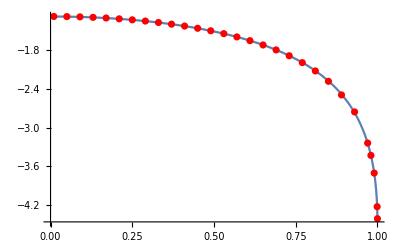

```mathematica
Show[Plot[nlmf[x],{x,0,1.2}],ListPlot[data1,PlotStyle->Red],PlotRange->All]
```

### Phases behaviour for | s | < ℓ < 40

#### Fitting 1

```mathematica
j1=0.9;
ω1=0.4;
modes1=ParallelTable[ReplaceParams[j1,-1,ℓ,𝓂,ω1]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[j1,-1,ℓ,𝓂,ω1,IncreasePrecision],{ℓ,1,50},{𝓂,{-1,0,1}}];
```

```mathematica
ticksArg1={TicksParse@{0,"-\\tfrac{\\pi}{2}","-\\pi","-\\tfrac{3\\pi}{2}"},TicksParse@(10Range[0,5])};
ticksF1={TicksParse@Range[0,1000,200],TicksParse@(Range[0,Pi,Pi/4])};
ticksFD1={TicksParse@Range[0,0.8,0.2],TicksParse@(Range[0,Pi,Pi/4])};
```

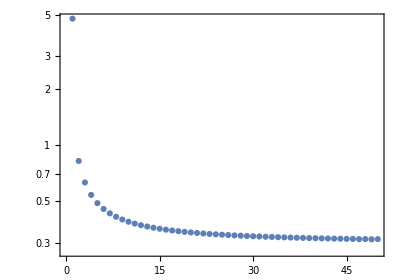
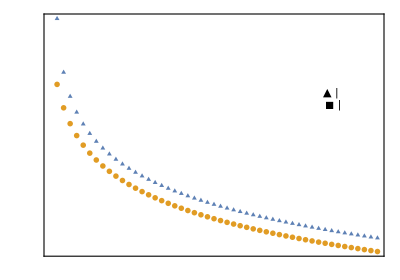
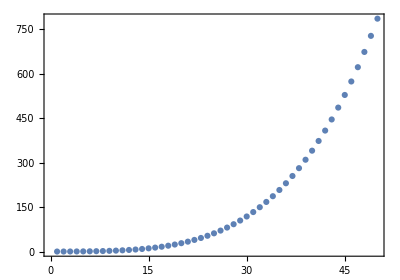
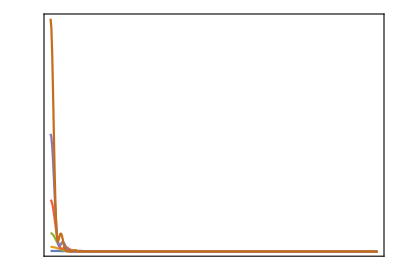
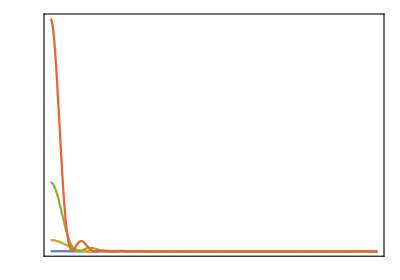
-Graphics- | -Graphics--Graphics- | -Graphics- | 
-Graphics--Graphics- |  | -Graphics--Graphics- |

```mathematica
δ1=-0.3;
lmaxFD1={8,16,24,32,40,48};
lmaxF1={4,8,12,16};
dataV1=Last[Flatten[modes1,{2}]]⟦;;50⟧;
funcV1=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[j1,-1,ℓ,1,ω1]@(dataV1⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV1⟦All,1⟧}];
funcV1noreg=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[j1,-1,ℓ,1,ω1]@(dataV1⟦ℓ,3⟧-1)SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV1⟦All,1⟧}];
argV1={Join[{#1,Arg@#3}&@@@dataV1⟦{1}⟧,Rest[{#1,g@Arg@#3}&@@@dataV1]],ReplaceParams[j1,-1,#1,1,ω1]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1]]}&@@@dataV1}//ListPlot[#,Joined->False,PlotRange->{All,Automatic},PlotMarkers->markers,plotDirs,FrameLabel->{TeX@"\\ell",""},FrameTicks->ticksArg,PlotLegends->Placed[legArg,{0.85,0.65}]]&//
Labeled[#,TeX["\\hspace{1.5cm}(\\mathscr{J}=0.9, \\bar{\\omega}=0.4, m=1)"],Top,Spacings->{0,-0.6}]&;;
diffV1=ReplaceParams[j1,-1,#1,1,ω1]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1]]//Abs}&@@@dataV1//ListLogPlot[#,Joined->False,plotDirs]&;
sumV1={Range[0,Pi,Pi/400],Abs[Total@funcV1[[1;;#]]]^2}ᵀ&/@lmaxFD1//ListPlot[#,Joined->True,PlotRange->All,plotDirs,PlotRangePadding->{0,0.02},FrameTicks->ticksFD1,FrameLabel->{TeX@"\\theta",None},PlotLegends->Placed[LineLegend[Automatic,TeX@lmaxFD1,LegendFunction->Panel,LegendLabel->TeX["\\ell_\\mathrm{max}"],LegendLayout->"Row"],{0.72,0.75}]]&//
Labeled[#,TeX["\\hspace{1.5cm} |f_\\mathrm{D}(\\theta, 0)|^2~~(\\mathscr{J}=0.9, \\bar{\\omega}=0.4)"],Top,Spacings->{0,-0.6}]&;
sumV1noreg={Range[0,Pi,Pi/400],Abs[Total@funcV1noreg[[1;;#]]]^2}ᵀ&/@lmaxF1//ListPlot[#,Joined->True,PlotRange->All,plotDirs,PlotRangePadding->{0,40},FrameTicks->ticksF1,FrameLabel->{TeX@"\\theta",None},
PlotLegends->Placed[LineLegend[Automatic,TeX@lmaxF1,LegendFunction->Panel,LegendLabel->TeX["\\ell_\\mathrm{max}"]],{0.88,0.62}]]&//
Labeled[#,TeX["\\hspace{1.5cm} |f(\\theta, 0)|^2~~(\\mathscr{J}=0.9, \\bar{\\omega}=0.4)"],Top,Spacings->{0,-0.6}]&;
{{diffV1,argV1,ListPlot[First@(Abs[Total@funcV1[[1;;#]]]^2)&/@Range[50],plotDirs],SpanFromLeft},{sumV1,SpanFromLeft,sumV1noreg,SpanFromLeft}}//Grid[#,Alignment->Left]&
Export[thesisPath<>"arg1.pdf",argV1];
Export[thesisPath<>"sumFD1.pdf",sumV1];
Export[thesisPath<>"sumF1.pdf",sumV1noreg];
```

#### Fitting 2

```mathematica
j2=0.99;
ω2=0.4;
modes2=ParallelTable[ReplaceParams[j2,-1,ℓ,𝓂,ω2]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[j2,-1,ℓ,𝓂,ω2,IncreasePrecision],{ℓ,1,50},{𝓂,{-1,0,1}}];
```

```mathematica
ticksArg2={TicksParse@{0,"-\\tfrac{\\pi}{2}","-\\pi","-\\tfrac{3\\pi}{2}","-2\\pi"},TicksParse@(10Range[0,5])};
ticksF2={TicksParse@Range[0,1000,200],TicksParse@(Range[0,Pi,Pi/4])};
ticksFD2={TicksParse@Range[0,1.6,0.2],TicksParse@(Range[0,Pi,Pi/4])};
```

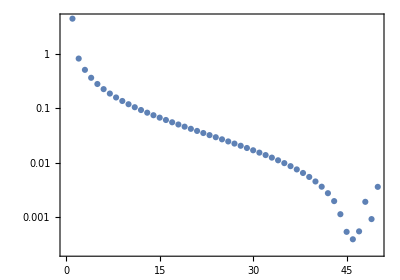
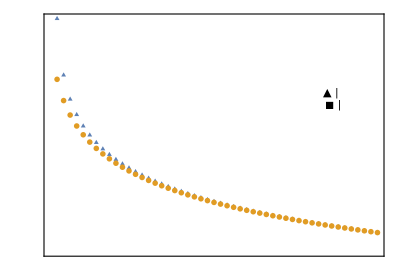
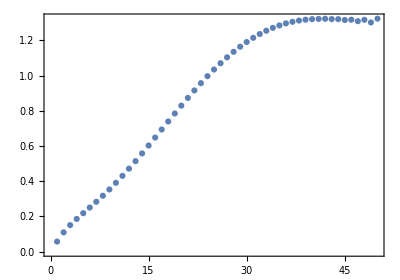
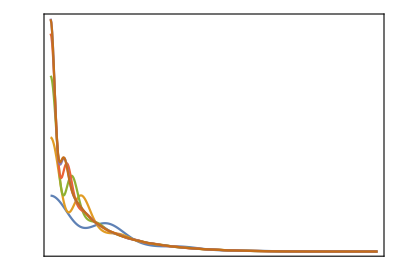
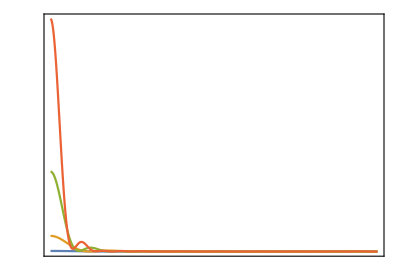
-Graphics- | -Graphics--Graphics- | -Graphics- | 
-Graphics--Graphics- |  | -Graphics--Graphics- |

Export::nodir: Directory D:\Jose\Downloads\Thesis\Figures\ does not exist.

Export::noopen: Cannot open Thesis\Figures\arg2.pdf.

Export::nodir: Directory D:\Jose\Downloads\Thesis\Figures\ does not exist.

Export::noopen: Cannot open Thesis\Figures\sumFD2.pdf.

Export::nodir: Directory D:\Jose\Downloads\Thesis\Figures\ does not exist.

Export::noopen: Cannot open Thesis\Figures\sumF2.pdf.

```mathematica
δ2=-0.182;
lmaxFD2={8,16,24,32,40,48};
lmaxF2={4,8,12,16};
dataV2=Last[Flatten[modes2,{2}]]⟦;;50⟧;
funcV2=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[j2,-1,ℓ,1,ω2]@(dataV2⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV2⟦All,1⟧}];
funcV2noreg=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[j2,-1,ℓ,1,ω2]@(dataV2⟦ℓ,3⟧-1)SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV2⟦All,1⟧}];
argV2={Join[{#1,Arg@#3}&@@@dataV2⟦{1}⟧,Rest[{#1,g@Arg@#3}&@@@dataV2]],ReplaceParams[j2,-1,#1,1,ω2]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2]]}&@@@dataV2}//ListPlot[#,Joined->False,PlotRange->{-2π,Automatic},PlotMarkers->markers,plotDirs,FrameLabel->{TeX@"\\ell",None},FrameTicks->ticksArg2,PlotLegends->Placed[legArg,{0.85,0.65}]]&//
Labeled[#,TeX["\\hspace{1.5cm} (\\mathscr{J}=0.99, \\bar{\\omega}=0.4, m=1)"],Top,Spacings->{0,-0.6}]&;;
diffV2=ReplaceParams[j2,-1,#1,1,ω2]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2]]//Abs}&@@@dataV2//ListLogPlot[#,Joined->False,plotDirs]&;
sumV2={Range[0,Pi,Pi/400],Abs[Total@funcV2[[1;;#]]]^2}ᵀ&/@lmaxFD2//ListPlot[#,Joined->True,PlotRange->All,plotDirs,PlotRangePadding->{0,0.05},FrameTicks->ticksFD2,FrameLabel->{TeX@"\\theta",None},PlotLegends->Placed[LineLegend[Automatic,TeX@lmaxFD2,LegendFunction->Panel,LegendLabel->TeX["\\ell_\\mathrm{max}"],LegendLayout->"Row"],{0.72,0.75}]]&//
Labeled[#,TeX["\\hspace{1.5cm} |f_\\mathrm{D}(\\theta, 0)|^2 ~~(\\mathscr{J}=0.99, \\bar{\\omega}=0.4)"],Top,Spacings->{0,-0.6}]&;
sumV2noreg={Range[0,Pi,Pi/400],Abs[Total@funcV2noreg[[1;;#]]]^2}ᵀ&/@lmaxF2//ListPlot[#,Joined->True,PlotRange->All,plotDirs,PlotRangePadding->{0,40},FrameTicks->ticksF2,FrameLabel->{TeX@"\\theta",None},
PlotLegends->Placed[LineLegend[Automatic,TeX@lmaxF2,LegendFunction->Panel,LegendLabel->TeX["\\ell_\\mathrm{max}"]],{0.88,0.62}]]&//
Labeled[#,TeX["\\hspace{1.5cm} |f(\\theta, 0)|^2 ~~(\\mathscr{J}=0.99, \\bar{\\omega}=0.4)"],Top,Spacings->{0,-0.6}]&;
{{diffV2,argV2,ListPlot[First@(Abs[Total@funcV2[[1;;#]]]^2)&/@Range[50],plotDirs],SpanFromLeft},{sumV2,SpanFromLeft,sumV2noreg,SpanFromLeft}}//Grid[#,Alignment->Left]&
Export[thesisPath<>"arg2.pdf",argV2];
Export[thesisPath<>"sumFD2.pdf",sumV2];
Export[thesisPath<>"sumF2.pdf",sumV2noreg];
```

#### Fitting 3

```mathematica
j3=0.8;
ω3=0.3;
modes3=ParallelTable[ReplaceParams[j3,-1,ℓ,𝓂,ω3]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[j3,-1,ℓ,𝓂,ω3,IncreasePrecision],{ℓ,1,50},{𝓂,{-1,0,1}}];
```

```mathematica
ticksArg3={TicksParse@{0,"-\\tfrac{\\pi}{2}","-\\pi","-\\tfrac{3\\pi}{2}"},TicksParse@(10Range[0,5])};
ticksF3={TicksParse@Range[0,300,100],TicksParse@(Range[0,Pi,Pi/4])};
ticksFD3={TicksParse@Range[0,0.5,0.1],TicksParse@(Range[0,Pi,Pi/4])};
```

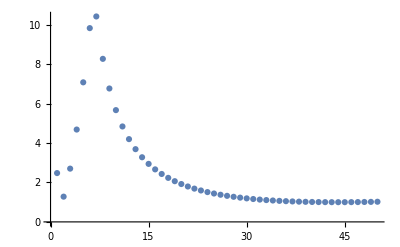

```mathematica
{#1,Cos[I Arg[#3]]}&@@@dataV1//Chop//ListPlot
```

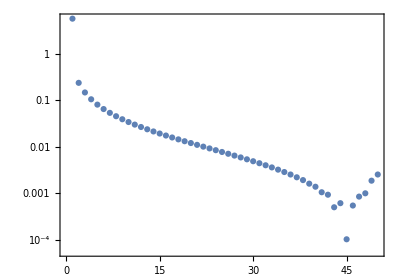
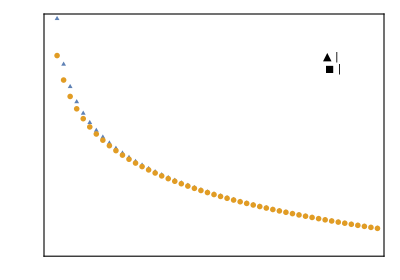
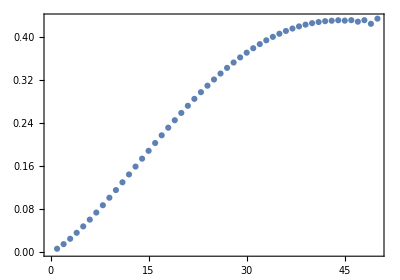
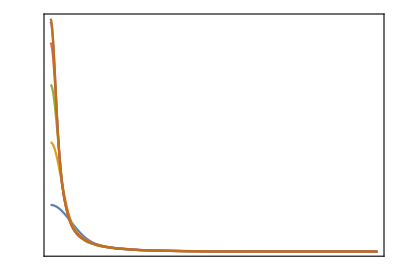
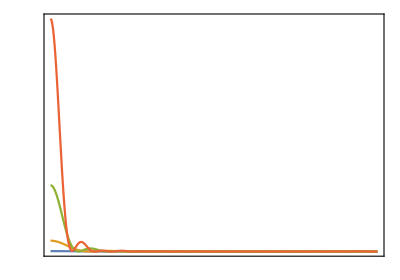
-Graphics- | -Graphics--Graphics- | -Graphics- | 
-Graphics--Graphics- |  | -Graphics--Graphics- |

```mathematica
δ3=-0.149;
lmaxFD3={8,16,24,32,40,48};
lmaxF3={4,8,12,16};
dataV3=Last[Flatten[modes3,{2}]]⟦;;50⟧;
funcV3=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[j3,-1,ℓ,1,ω3]@(dataV3⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV3⟦All,1⟧}];
funcV3noreg=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[j3,-1,ℓ,1,ω3]@(dataV3⟦ℓ,3⟧-1)SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV3⟦All,1⟧}];
argV3={Join[{#1,Arg@#3}&@@@dataV3⟦{1}⟧,Rest[{#1,g@Arg@#3}&@@@dataV3]],ReplaceParams[j3,-1,#1,1,ω3]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3]]}&@@@dataV3}//ListPlot[#,Joined->False,PlotRange->{-Pi-0.3,Automatic},PlotMarkers->markers,plotDirs,FrameLabel->{TeX@"\\ell",None},FrameTicks->ticksArg,PlotLegends->Placed[legArg,{0.85,0.80}]]&//
Labeled[#,TeX["\\hspace{1.5cm}(\\mathscr{J}=0.8, \\bar{\\omega}=0.3, m=1)"],Top,Spacings->{0,-0.6}]&;
diffV3=ReplaceParams[j3,-1,#1,1,ω3]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3]]//Abs}&@@@dataV3//ListLogPlot[#,Joined->False,plotDirs]&;
sumV3={Range[0,Pi,Pi/400],Abs[Total@funcV3[[1;;#]]]^2}ᵀ&/@lmaxFD3//ListPlot[#,Joined->True,PlotRange->All,plotDirs,PlotRangePadding->{0,0.02},FrameTicks->ticksFD3,FrameLabel->{TeX@"\\theta",None},PlotLegends->Placed[LineLegend[Automatic,TeX@lmaxFD3,LegendFunction->Panel,LegendLabel->TeX["\\ell_\\mathrm{max}"],LegendLayout->"Row"],{0.72,0.75}]]&//
Labeled[#,TeX["\\hspace{1.5cm} |f_\\mathrm{D}(\\theta, 0)|^2 ~~(\\mathscr{J}=0.8, \\bar{\\omega}=0.3)"],Top,Spacings->{0,-0.6}]&;
sumV3noreg={Range[0,Pi,Pi/400],Abs[Total@funcV3noreg[[1;;#]]]^2}ᵀ&/@lmaxF3//ListPlot[#,Joined->True,PlotRange->All,plotDirs,PlotRangePadding->{0,40},FrameTicks->ticksF3,FrameLabel->{TeX@"\\theta",None},
PlotLegends->Placed[LineLegend[Automatic,TeX@lmaxF3,LegendFunction->Panel,LegendLabel->TeX["\\ell_\\mathrm{max}"]],{0.88,0.62}]]&//
Labeled[#,TeX["\\hspace{1.5cm} |f(\\theta, 0)|^2 ~~(\\mathscr{J}=0.8, \\bar{\\omega}=0.3)"],Top,Spacings->{0,-0.6}]&;
{{diffV3,argV3,ListPlot[First@(Abs[Total@funcV3[[1;;#]]]^2)&/@Range[50],plotDirs],SpanFromLeft},{sumV3,SpanFromLeft,sumV3noreg,SpanFromLeft}}//Grid[#,Alignment->Left]&
Export[thesisPath<>"arg3.pdf",argV3];
Export[thesisPath<>"sumFD3.pdf",sumV3];
Export[thesisPath<>"sumF3.pdf",sumV3noreg];
```

#### More testing

```mathematica
modes4=ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.99,-1,Sequence@@Echo[{ℓ,𝓂}],0.4,IncreasePrecision],{ℓ,1,40},{𝓂,-ℓ,ℓ}];
```

```mathematica
{0.99,0.4,#1,#2,Re@#3,Im@#3}&@@@Flatten[modes4,{1,2}]//Export["Zratio.csv",#]&
```

Zratio.csv

```mathematica
δ4=-0.18;
dataV4=modes4;
{θ0,ϕ0}={0.3,0};
funcV4pos=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ+𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,-1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
funcV4neg=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ-𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
```

```mathematica
funcV4pos0=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ+𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
funcV4neg0=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ-𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,-1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
```

```mathematica
sumV4={Range[0,Pi,Pi/400],Abs[Total@funcV4pos[[1;;#]]]^2+Abs[Total@funcV4neg[[1;;#]]]^2}ᵀ&/@{40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
sumV40={Range[0,Pi,Pi/400],Abs[Total@funcV4pos0[[1;;#]]]^2+Abs[Total@funcV4neg0[[1;;#]]]^2}ᵀ&/@{40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large,PlotStyle->Red]&;
```

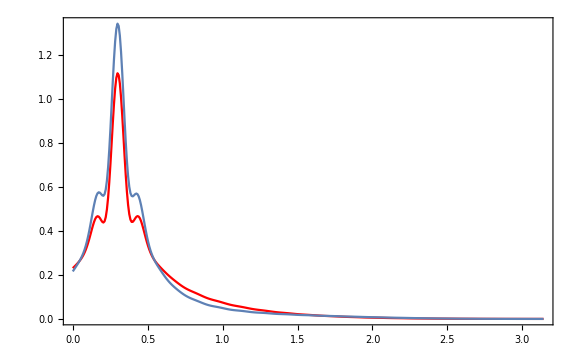

```mathematica
Show[sumV40,sumV4,PlotRange->All]
```

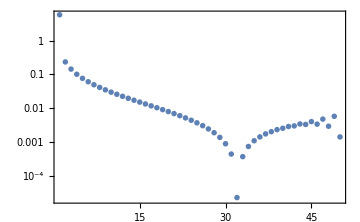
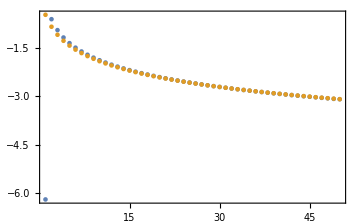
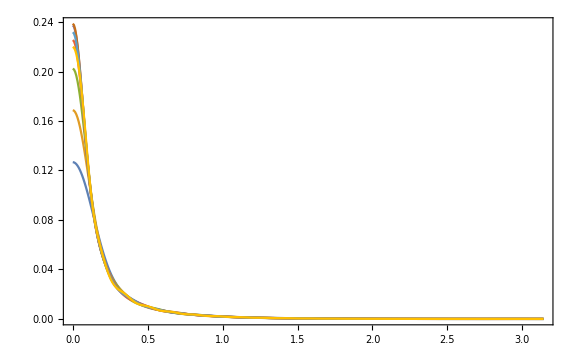
-Graphics- | -Graphics-
-Graphics- |

```mathematica
argV4={{#1,g@Arg@#3}&@@@dataV3,ReplaceParams[0.99,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4]]}&@@@dataV4}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV4=ReplaceParams[0.8,-1,#1,1,0.3]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4]]//Abs}&@@@dataV4//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV4={Range[0,Pi,Pi/400],Abs[Total@funcV4[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV4,argV4},{sumV4,SpanFromLeft}}//Grid
```

### Phases testing

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ArgToLine=#-Accumulate@Join[{0},2π Boole@Thread[Abs[#⟦1;;-2⟧-#⟦2;;All⟧]>0.80Pi]]&;
```

```mathematica
numArg=Import["Data/phaseNumerical32.csv"];
thArg=List@@({#ᵀ⟦1⟧,#ᵀ⟦2⟧,2 Arg[Gamma[32+1-2 ⅈ #ᵀ⟦2⟧/(#ᵀ⟦1⟧+√(1-(#ᵀ⟦1⟧)^2)) ]]//ArgToLine//ArgToLine}ᵀ&/@GroupBy[numArg⟦All,{1,2}⟧,First->Identity])//Flatten[#,1]&;
```

```mathematica
diffArg=Transpose[thArgᵀ-({0,0,#3}&@@@numArg)ᵀ];
```

```mathematica
diffGroupJ=GroupBy[diffArg,First->Rest];
diffGroupW=GroupBy[diffArg,(#[[2]]&)->(#[[{1,3}]]&)];
```

```mathematica
nlmf0=NonlinearModelFit[diffArg,a(𝓌 𝒿)/(1+Sqrt[1-𝒿^2])+b((𝓌 𝒿)/(1+Sqrt[1-𝒿^2]))^2+c 𝓌/(1+Sqrt[1-𝒿^2])+d 𝓌/(1+Sqrt[1-𝒿^2]) Log[𝓌/(1+Sqrt[1-𝒿^2])]+e,{a,b,c,d,{e,0}},{𝒿,𝓌}];
nlmf0["ParameterTable"]
{Show[
ListPointPlot3D[diffArg],
Plot3D[nlmf0[𝒿,𝓌],{𝒿,0,1},{𝓌,0,1.5}],
AxesLabel->(Style[#,FontSize->15,FontWeight->Bold,FontColor->Black]&/@{"𝒿","ω̄","2 (δ_(32, 1)-δ_32^N)"}),
ImageSize->Large,
FrameStyle->BlackFrame],
ListPointPlot3D[{#1,#2,#3/nlmf0[#1,#2]-1}&@@@diffArg,ImageSize->Medium]}
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 15.2112 | 0.0249427 | 609.846 | 3.2369487743×10^-8316
b | -1.14045 | 0.0277283 | -41.1294 | 1.8836423×10^-343
c | -14.835 | 0.0118334 | -1253.65 | 3.1177681013×10^-11616
d | 0.233227 | 0.0255216 | 9.13841 | 7.48106×10^-20
e | 0.0531117 | 0.00698657 | 7.60196 | 3.16083×10^-14

{-Graphics3D-,-Graphics3D-}

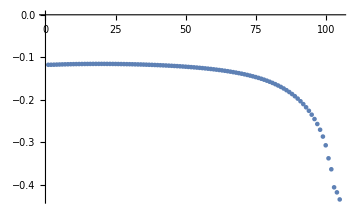
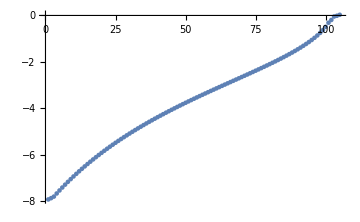
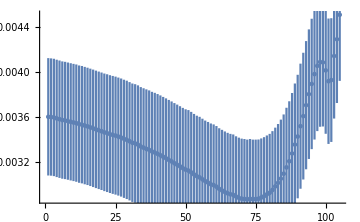
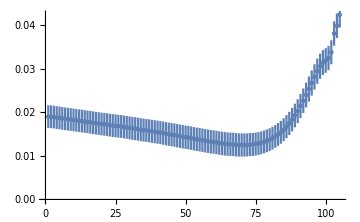

```mathematica
nlmfJ=ParallelTable[NonlinearModelFit[diffGroupJ⟦i⟧,c+b 𝓌+a 𝓌^2+d 𝓌 Log[𝓌],{a,b,c,d},𝓌],{i,Length@diffGroupJ}];
Transpose[{{a,b,c,d},#["ParameterErrors"]}/.#["BestFitParameters"]]&/@nlmfJ//Transpose//Map[ErrorListPlot[#,PlotRange->All,ImageSize->Medium]&]
```

```mathematica
Needs["ErrorBarPlots`"]
```

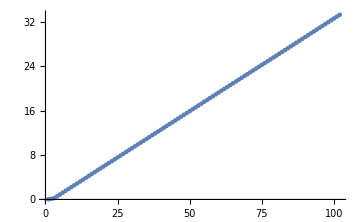
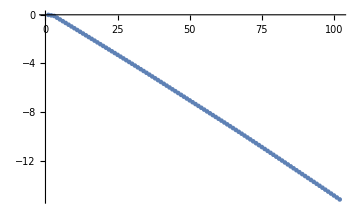
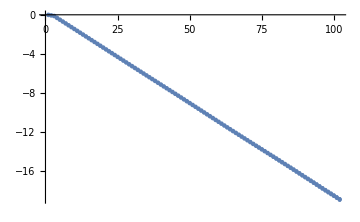
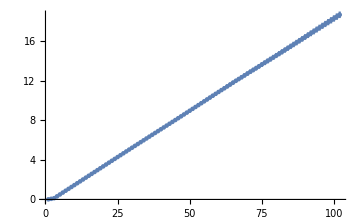

```mathematica
nlmfW=ParallelTable[NonlinearModelFit[diffGroupW⟦i⟧,a 𝒿/(1+Sqrt[1-𝒿^2])+b(𝒿/(1+Sqrt[1-𝒿^2]))^2+c(1+Sqrt[1-𝒿^2])+d (1+Sqrt[1-𝒿^2]) Log[1+Sqrt[1-𝒿^2]],{a,b,c,d},𝒿],{i,Length@diffGroupW}];
Transpose[{{a,b,c,d},#["ParameterErrors"]}/.#["BestFitParameters"]]&/@nlmfW//Transpose//Map[ErrorListPlot[#,PlotRange->All,ImageSize->Medium]&]
```

### Gravitational ℓ=𝓂=2

```mathematica
Zgr=GroupBy[Import[GetZFile[2,2,2,"bothPrecision"]][[4;;]],N@*Rationalize@*First->Rest];
```

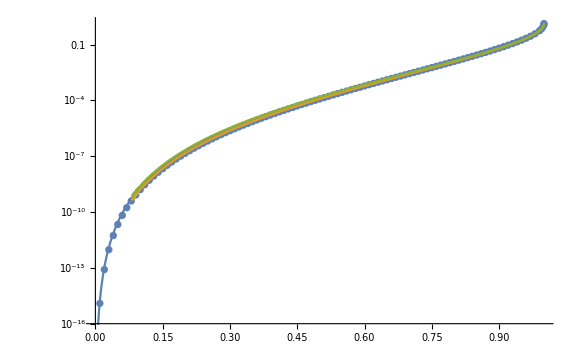
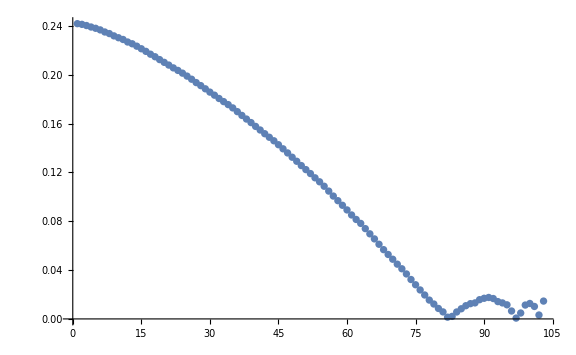

```mathematica
maxAmp=Mean/@(MaximalBy[Mean[#1⟦{2,3}⟧]&]/@Zgr)⟦All,1,{2,3}⟧;
maxAmpNlmf=NonlinearModelFit[KeyValueMap[List]@maxAmp,a ((1-√(1-𝒿^2))/(1+√(1-𝒿^2)))^3 Exp[b 𝒿],{a,b},𝒿];
{Show[
ListLogPlot[maxAmp,PlotRange->All],
LogPlot[{maxAmpNlmf[𝒿],maxAmpNlmf["MeanPredictionBands",ConfidenceLevel->0.99]}//Evaluate,{𝒿,0,1},PlotRange->All],
ImageSize->Large
],
ListPlot[Abs[Values@maxAmp/(maxAmpNlmf/@Keys@maxAmp)-1],ImageSize->Large]}
```

```mathematica
Show[
{#1,#2/#1,Mean[{#3,#4}]}&@@@Import[GetZFile[2,2,2,"bothPrecision"]][[4;;]]//ListPlot3D[#,PlotRange->All]&,Graphics3D[{Black,Thick,Line@KeyValueMap[{#1,#2⟦1,1⟧,#2⟦1,2⟧}&]@(MaximalBy[Mean[#1⟦{2,3}⟧]&]/@Zgr)}],
AxesLabel->(Style[#,FontSize->15,FontWeight->Bold,FontColor->Black]&/@{"𝒿","ω̄","Z_(2, 2)"}),
ImageSize->Large,
FrameStyle->BlackFrame
]
```

-Graphics3D-